# Lucas Rudd Math Methods Project

Part I & II

```mathematica
Clear[n,i,s,r,k,b,h,ds,di,dr,r,s,i,tab1,tab2,tab3,iw,sw,rw,dsw,diw,drw,tab1w,tab2w,tab3w]
```

(*ds/dt is given. di/dt can be represented by saying that the number of infected people will change depending on the number of suceptible people, the number of infected people and how many people the infected run into per unit time, however we must subtract the number of recorved people from this. dr/dt is the change in recovred people, and this is just the recovery probability k times the amount of currently infected people. the total number of recoverd people r can be modeled by the previous amount of recovered people plus the step size times the change in recovered people per unit time. The total number of suceptilbe people can be modeled by the previous number of suceptible people times the change in suceptible people per unit time. The number of infected people is the previous amount of infected plus the change in the number of infected people per unit time.*)

```mathematica
ss[m_,a_,j_]:=
Module[{ds,di,dr,r,s,i,b,k,e},
b=m;k=a;e=j;n=3*10^6;i[0]=e/n;s[0]=n/n-i[0];r[0]=0;h=.1;
ds[t_]:=ds[t]=-b(s[t])(i[t]);
di[t_]:=di[t]=(b(s[t])(i[t])-dr[t]); 
dr[t_]:=dr[t]=k(i[t]);
r[t_]:=r[t]=r[t-1]+h(dr[t-1]);
s[t_]:=s[t]=(s[t-1]+h(ds[t-1])); 
i[t_]:=i[t]=(i[t-1]+h(di[t-1]));
tab1 = Table[s[t],{t,0,170}];
tab2 = Table[i[t],{t,0,170}];
tab3 = Table[r[t],{t,0,170}];
Print["b = ", m];
Print["k = ", a];
Print["i[0] = ", j];
ListLinePlot[{tab1,tab2,tab3},AxesLabel->Proportion]]
```

b = 3

k = 1

i[0] = 10

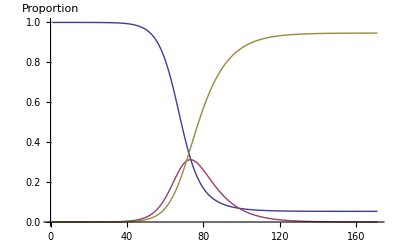

b = 2

k = 1/3

i[0] = 10

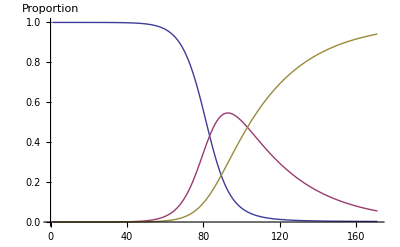

b = 8

k = 1/9

i[0] = 10

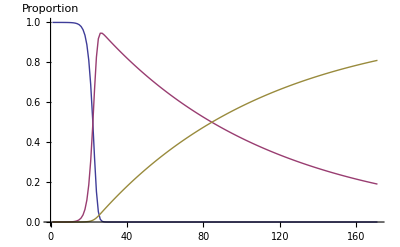

b = 10

k = 1

i[0] = 10

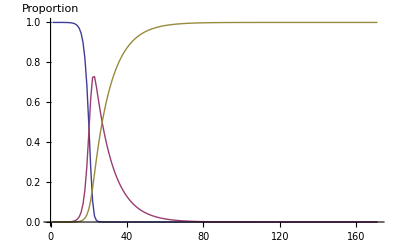

b = 5/2

k = 1/2

i[0] = 10

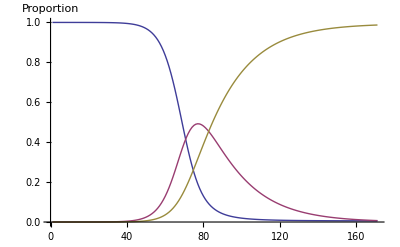

```mathematica
ss[3,1,10]
ss[2,(1/3),10]
ss[8,(1/9),10]
ss[10,1,10]
ss[5/2,1/2,10]
```

(*The infection will be well contained if the amount of people who catch the disease per unit time (b) is small, and if the recovery rate (k) is large. Likewise, the disease will not be well contained if the amount of people who catch the disease per unit time (b) is large, and if the recovery rate (k) is very small. I chose a variety of b and k values to show this relationship. In fact, if k is larger than or equal to b then the recovery rate is faster than the infection rate and very little, if any, people get sick*)

## Part III

A)

(*comparing the graphs above to the graphs forthcoming I will show how the inital value i[0] effects the peak infection rate by making it occur sooner, and logically it would make sense to say that i[0] effects the peak value of infection due to the fact that more people have the disease initally*)

b = 3

k = 1

i[0] = 10

-Graphics-

b = 3

k = 1

i[0] = 100

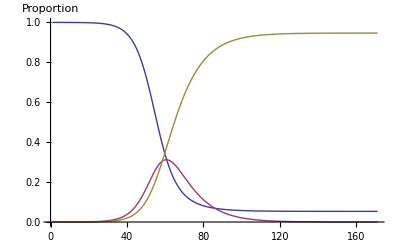

b = 3

k = 1

i[0] = 1000

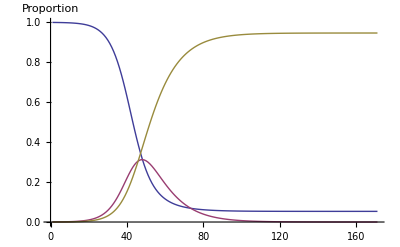

b = 3

k = 1

i[0] = 1000000

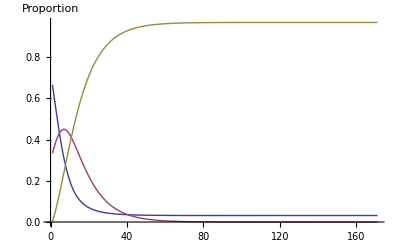

```mathematica
ss[3,1,10]
ss[3,1,100]
ss[3,1,1000]
ss[3,1,1000000]
```

(*it is clear that the more inital sick people there are the quicker the peak infection rate happens and, although subtly, the greater the maximum number of infected people*)

B)

The total number of infected people ought to be equal to the amount of recovered people after a very very long time

```mathematica
n=3*10^6;i[0]=10/n;s[0]=n/n-i[0];r[0]=0;h=.1;b=2;k=1/3;
ds[t_]:=ds[t]=-b(s[t])(i[t]);
di[t_]:=di[t]=(b(s[t])(i[t])-dr[t]); 
dr[t_]:=dr[t]=k(i[t]);
r[t_]:=r[t]=r[t-1]+h(dr[t-1]);
s[t_]:=s[t]=(s[t-1]+h(ds[t-1])); 
i[t_]:=i[t]=(i[t-1]+h(di[t-1]));
Print["The total number of infected people is: ",n(r[150])]
```

The total number of infected people is: 2.6666×10^6

C)

(*The value of ds/dt+di/dt+dr/dt should be zero because the change in suceptible people should be equal to the change in infected people plus the change in recovered people if the poluation is to stay constant. We could also look at the equations above and see that ds[t] is exactly equal to di[t]+dr[t]*)

```mathematica
ds[1]+di[1]+dr[1]
```

2.11758×10^-22

(*however, we can get a number which is not quite zero for some value of t, but although this number is not zero it is very very small. This is because we are using discretization tequniques and are approximating these values. However, 10^-22 is a VERY small number and can be said to be zero*)

```mathematica
ds[120]+di[120]+dr[120]
```

0.

## Part IV

(*ds/dt will be the same equation but subtracting the suceptible people who die and also adding new suceptible people who are born, di/dt will be the same equation as above, but subtracting infected people who die, likewise, dr/dt will be the same equation but subtracting recovered people who die. People being born will not affect the S,I,or R equations other than the fact that the derivatives will change slightly. However, because new people are being introduced it is expected that the total number of recovered people will be greater than the inital population. It is also expected that the total number of infected individuals will level out at a slightly higer proportion because there are constanly new people to infect.*)

```mathematica
ssw[x_,y_,z_]:=Module[{dsw,diw,drw,rw,sw,iw,b,k,e},n=3*10^6;iw[0]=e/n;sw[0]=n/n-iw[0];rw[0]=0;h=.1;b=x;k=y;e=z;w=200000/n;
dsw[t_]:=dsw[t]=w-b(sw[t])(iw[t])-w(sw[t]);
diw[t_]:=diw[t]=(b(sw[t])(iw[t])-drw[t]-w(iw[t]));
drw[t_]:=drw[t]=k(iw[t])-w(rw[t]);
rw[t_]:=rw[t]=rw[t-1]+h(drw[t-1]);
sw[t_]:=sw[t]=(sw[t-1]+h(dsw[t-1])); 
iw[t_]:=iw[t]=(iw[t-1]+h(diw[t-1]));
tab1w = Table[sw[t],{t,0,170}];
tab2w = Table[iw[t],{t,0,170}];
tab3w = Table[rw[t],{t,0,170}];
Print["BIRTH/DEATH GRAPH:"];
Print["b = ", x];
Print["k = ", y];
Print["i[0] = ", z];
ListLinePlot[{tab1w,tab2w,tab3w}, AxesLabel->Proportion]]
```

b = 3

k = 1

i[0] = 10

-Graphics-

BIRTH/DEATH GRAPH:

b = 3

k = 1

i[0] = 10

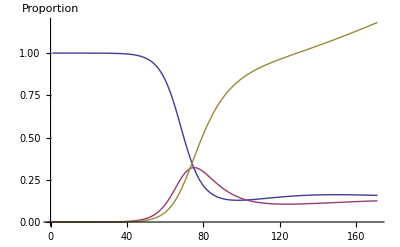

b = 5/2

k = 1/2

i[0] = 10

-Graphics-

BIRTH/DEATH GRAPH:

b = 5/2

k = 1/2

i[0] = 10

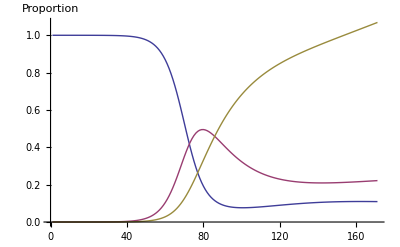

```mathematica
ss[3,1,10]
ssw[3,1,10]
ss[5/2,1/2,10]
ssw[5/2,1/2,10]
```

(*Although these graphs have an immensly large value for w (the death/birth rate) and is totally unrealistic, it was done to show the subtle changes in s, i, and r over time.*)